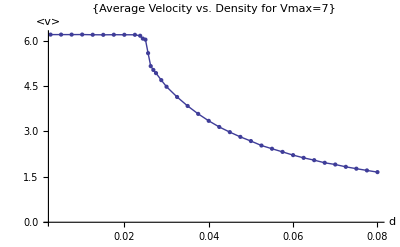

```mathematica
vbar7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax7.txt",{Number,Number}];
a=ListPlot[vbar7,PlotLabel->{"Average Velocity vs. Density for Vmax=7"},AxesLabel->{d,"<v>"},PlotRange->Full];
b=ListLinePlot[vbar7,PlotLabel->{"Average Velocity vs. Density for Vmax=7"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a,b]
```

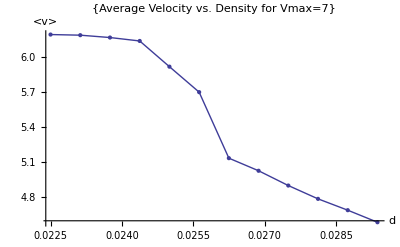

```mathematica
vbar72=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax7.fine.txt",{Number,Number}];
a2=ListPlot[vbar72,PlotLabel->{"Average Velocity vs. Density for Vmax=7"},AxesLabel->{d,"<v>"},PlotRange->Full];
b2=ListLinePlot[vbar72,PlotLabel->{"Average Velocity vs. Density for Vmax=7"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a2,b2]
```

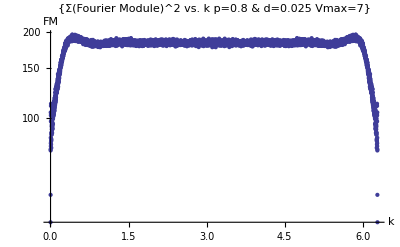

```mathematica
lsqdsum080125v7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/fourier.1d.averaged.d0.0225.p0.8.u.check.v7.uniform.txt",{Number,Number}];
ListLogPlot[lsqdsum080125v7,PlotLabel->{"Σ(Fourier Module)^2 vs. k  p=0.8 & d=0.025 Vmax=7"},AxesLabel->{k,FM},PlotRange->Full]
```

```mathematica
vbar7
```

{{0.0025,6.2003},{0.005,6.20035},{0.0075,6.2001},{0.01,6.20188},{0.0125,6.19524},{0.015,6.1927},{0.0175,6.19635},{0.02,6.19458},{0.0225,6.19382},{0.02375,6.16187},{0.024375,6.0684},{0.025,6.0344},{0.025625,5.58758},{0.02625,5.1586},{0.026875,5.03256},{0.0275,4.92771},{0.02875,4.69623},{0.03,4.47767},{0.0325,4.13916},{0.035,3.84177},{0.0375,3.58082},{0.04,3.35059},{0.0425,3.14826},{0.045,2.97742},{0.0475,2.82066},{0.05,2.68288},{0.0525,2.53524},{0.055,2.42864},{0.0575,2.32461},{0.06,2.21801},{0.0625,2.12794},{0.065,2.05126},{0.0675,1.96479},{0.07,1.90769},{0.0725,1.83132},{0.075,1.76995},{0.0775,1.71228},{0.08,1.65617}}

```mathematica
vbar72
```

{{0.0225,6.19321},{0.023125,6.18782},{0.02375,6.16764},{0.024375,6.13831},{0.025,5.91853},{0.025625,5.70055},{0.02625,5.13571},{0.026875,5.0279},{0.0275,4.9015},{0.028125,4.78753},{0.02875,4.69064},{0.029375,4.58744}}